In this notebook we often use σ = δ^-1

### Set file location and pastel color pallet

```mathematica
fileLocation = "/Users/andrewgoetz/Documents/Chemosensing_Plots";
pOrange = RGBColor["#FFCC2A"];
pPurple = RGBColor["#C8B6FF"];
pGreen = RGBColor["#B1F9A4"];
pRed = RGBColor["#FFAAAC"];
pJade = RGBColor["#95D3BE"];
pBlue = RGBColor["#1CEAFF"];
pPink = RGBColor["#F08AFF"];
```

### Analytical Model

```mathematica
Clear[kprod,kn1,k1,L,ki,kis,R,B,u,Dr,kdiff,γ,μ,β,R0,λ,g]
kprod = R0*ki;
kis = β*ki;
k1 = kn1/λ;
kn1 = ki*μ;
L = u*kn1/k1;
kdiff = 4*ki*γ;
(*Factor of 4 arises from discretization*)
(*kdiff = D/((L/2)^2)
gamma = D/(L^2*ki)
kdiff = 4D/L^2
kdiff /(4*ki) = D/(L^2*ki) = gamma
kdiff = 4*ki*gamma
*)
kdiffs = kdiff*σ;
R1ss = kprod+B1*kn1-R1*(ki+L*k1)-R1*kdiff+R2*kdiff==0;
R2ss = kprod+B2*kn1-R2*(ki+L*k1*(1+g))-R2*kdiff+R1*kdiff==0;
B1ss = -B1*kn1+R1*(L*k1)-B1*kis-B1*kdiffs+B2*kdiffs==0;
B2ss = -B2*kn1+R2*(L*k1*(1+g))-B2*kis-B2*kdiffs+B1*kdiffs==0;
analyticSol2 = Solve[{R1ss,R2ss,B1ss,B2ss},{R1,B1,R2,B2}];
(*Obtains a symbolic expression for the ARP*)
fullPerformance = Assuming[{β>0,γ>0,σ>0,δ>0,R0==1},FullSimplify[(analyticSol2[[1]][[4]][[2]]-analyticSol2[[1]][[2]][[2]])]];
(*Here we assume shallow gradient and rapid ligand binding mechanics*)
analytical = FullSimplify[Limit[Series[fullPerformance,{g,0,1}],μ->∞]]
```

(g u (1+8 γ))/((1+u β) (1+8 γ+u (β+8 γ σ)))

```mathematica
(*Solves for the optimal background*)
optMu = Assuming[{β>0,γ>0,σ>0,δ>0},FullSimplify[Solve[D[analytical,u]==0,u][[2]][[1]][[2]]]]
```

√((1+8 γ)/(β^2+8 β γ σ))

```mathematica
(*Full analytical ARP*)
optPerf = Assuming[{β>0,γ>0,σ>0,δ>0},FullSimplify[analytical/.u->optMu]];
(*Full analytical ARP_n*)
optRelPerf = Assuming[{β>0,γ>0,σ>0,δ>0},FullSimplify[((optPerf))/(optPerf/.{γ->0})]];
(*The analytical ARP_n is monotonically increasing, note beta >= sigma*)
optPerfGammaDer = FullSimplify[D[optRelPerf,γ]];
(*Approximates ARP_n under slow diffusion*)
Assuming[{β>=1,γ>0,σ>0,δ>0},FullSimplify[Series[optRelPerf,{γ,0,1}]]]
(*Approximates ARP_n under fast diffusion*)
Assuming[{β>=1,γ>0,σ>0,δ>0},FullSimplify[((Limit[optRelPerf,γ->∞]))]]
```

1+(4-(4 σ)/β) γ+O[γ]^2

Limit::alimv: Warning: Assumptions that involve the limit variable are ignored.

(4 β)/(β+σ+2 √(β σ))

### Define Equations

```mathematica
Clear[kprod,kn1,k1,L,ki,kis,R,B,u,Dr,kdiff,γ,μ,β,R0,λ,g]
(*Profile generates the profile in receptor levels along the cell following our base model*)
Profile[β0_?NumericQ,γ0_?NumericQ,σ0_,g0_,u00_?NumericQ,μ0_,umax_,Lc0_?NumericQ]:=
(Pug[l_?NumericQ,u0def_?NumericQ,gdef_?NumericQ] := u0def+gdef*l;
Prss=0==1-pr[l]+μ*(pb[l]-(Pug[l,u0,g])*pr[l])+γ*D[pr[l],l,l];
Pbss=0==-β*pb[l]+μ*((Pug[l,u0,g])*pr[l]-pb[l])+γ*σ*D[pb[l],l,l];
g0effnew = g0*Lc0;
pofilesol=NDSolveValue[{Prss,Pbss}/.{β-> β0,γ->γ0,g->g0effnew,σ->σ0,u0->u00,μ->μ0}, {pr,pb}, {l} ∈Line[{{0},{1}}]];
pofilesol)

(*ProfileBasal generates the profile in receptor levels along the cell using the perfectly adaptive model*)
ProfileBasal[ki0_?NumericQ,kis0_?NumericQ,kprod0_?NumericQ,g0_?NumericQ,kphi0_?NumericQ,kub0_?NumericQ,kb0_?NumericQ,Dr0_?NumericQ,Db0_?NumericQ,u00_?NumericQ,Lc0_?NumericQ]:=
(ug[l_?NumericQ,u0def_?NumericQ,gdef_?NumericQ] := u0def+gdef*l;
rss=0==kprod-ki*r[l]-kphi*r[l]+kub*(b[l]-ug[l,u0,g]*r[l])+Dr/Lc^2*D[r[l],l,l];
bss=0==-kis*b[l]+kphi*r[l]+(ug[l,u0,g]*r[l]-b[l])*kub+Db/Lc^2*D[b[l],l,l];
g0eff = g0*Lc0;
dmwRbsol=Quiet[NDSolveValue[{rss,bss}/.{kprod-> kprod0,ki->ki0,kub->kub0,kb->kb0,Dr->Dr0,Db->Db0,Lc->Lc0,kis->kis0,kphi->kphi0,g->g0eff,u0->u00}, {r,b}, {l} ∈Line[{{0},{1}}]]];
dmwRbsol[[2]])

(*singleValue generates a single value for a cell parameter set assuming our base model. The value can be: b(1)-b(0) = "difference", b(0) = "LHS", b(1) = "RHS", or the average response along the cell "average". This value is weighted by one of 4 values: 1/beta = "Max", b(0) = "LHS", 1 = "None", b(0.5) = "Mid"*)
singleValue[β0_?NumericQ,γ0_?NumericQ,σ0_,g0_?NumericQ,u00_?NumericQ,μ0_,umax_,Lc0_?NumericQ,weight_,type_]:=
(ug[l_?NumericQ,u0def_?NumericQ,gdef_?NumericQ] := u0def+gdef*l;
rss=0==1-r[l]+μ*(b[l]-ug[l,u0,g]*r[l])+γ*D[r[l],l,l];
bss=0==-β*b[l]+μ*(ug[l,u0,g]*r[l]-b[l])+γ*σ*D[b[l],l,l];
g0eff = g0*Lc0;
dmwRbsol=Quiet[NDSolveValue[{rss,bss}/.{β-> β0,γ->γ0,g->g0eff,σ->σ0,u0->u00,μ->μ0}, {r,b}, {l} ∈Line[{{0},{1}}]]];
dmwrbbsol[l_] := dmwRbsol[[2]][l];
dmwrbsolmax=Quiet[NDSolveValue[{rss,bss}/.{β-> β0,γ->γ0,g->0,σ->σ0,u0->umax,μ->μ0}, {r,b}, {l} ∈Line[{{0},{1}}]]];
(*dmwrbbmaxtot = NIntegrate[dmwrbsolmax[[2]][l],{l,0,1}];*);
(*For max signal, all receptors are bound to ligand. The response is then just the production rate over the bound receptor degredation rate which, since 
kprod/ki = 1, kprod/ki* = 1/beta*);
weighting = Switch[weight,"Max",1/β0,"LHS",dmwrbbsol[0],"None",1,"Mid",dmwrbbsol[0.5]];
Switch[type,"difference",(dmwrbbsol[1]-dmwrbbsol[0])/weighting,"LHS",dmwrbbsol[0]/weighting,"RHS",dmwrbbsol[1]/weighting,"average",NIntegrate[dmwRbsol[[2]][l],{l,0,1}]/weighting])

(*singleValueBasal generates a single value for a cell parameter set using our perfectly adaptive model. The value can be: b(1)-b(0) = "difference", b(0) = "LHS", b(1) = "RHS", or the average response along the cell "average". This value is weighted by one of 4 values: 1/beta = "Max", b(0) = "LHS", 1 = "None", b(0.5) = "Mid"*)
singleValueBasal[ki0_?NumericQ,kis0_?NumericQ,kprod0_?NumericQ,g0_?NumericQ,kphi0_?NumericQ,kub0_?NumericQ,kb0_?NumericQ,Dr0_?NumericQ,Db0_?NumericQ,u00_?NumericQ,Lc0_?NumericQ,umax_?NumericQ,weight_,type_]:=
(ug[l_?NumericQ,u0def_?NumericQ,gdef_?NumericQ] := u0def+gdef*l;
rss=0==kprod-ki*r[l]-kphi*r[l]+kub*(b[l]-ug[l,u0,g]*r[l])+Dr/Lc^2*D[r[l],l,l];
bss=0==-kis*b[l]+kphi*r[l]+(ug[l,u0,g]*r[l]-b[l])*kub+Db/Lc^2*D[b[l],l,l];
g0eff = g0*Lc0;
dmwRbsol=Quiet[NDSolveValue[{rss,bss}/.{kprod-> kprod0,ki->ki0,kub->kub0,kb->kb0,Dr->Dr0,Db->Db0,Lc->Lc0,kis->kis0,kphi->kphi0,g->g0eff,u0->u00}, {r,b}, {l} ∈Line[{{0},{1}}]]];
dmwrbbsol[l_] := dmwRbsol[[2]][l];
dmwrbsolmax=Quiet[NDSolveValue[{rss,bss}/.{kprod-> kprod0,ki->ki0,kub->kub0,kb->kb0,Dr->Dr0,Db->Db0,Lc->Lc0,kis->kis0,kphi->kphi0,g->0,u0->umax0}, {r,b}, {l} ∈Line[{{0},{1}}]]];
(*dmwrbbmaxtot = NIntegrate[dmwrbsolmax[[2]][l],{l,0,1}];*);
(*For max signal, all receptors are bound to ligand. The response is then just the production rate over the bound receptor degredation rate which, since 
kprod/ki = 1, kprod/ki* = 1/beta*);
weighting = Switch[weight,"Max",1/β0,"LHS",dmwrbbsol[0],"None",1,"Mid",dmwrbbsol[0.5]];
Switch[type,"difference",(dmwrbbsol[1]-dmwrbbsol[0])/weighting,"LHS",dmwrbbsol[0]/weighting,"RHS",dmwrbbsol[1]/weighting,"average",NIntegrate[dmwRbsol[[2]][l],{l,0,1}]/weighting])

(*singleValueDimer generates a single value for a cell parameter set using our dimer model. The value can be: b(1)-b(0) = "difference", b(0) = "LHS", b(1) = "RHS", or the average response along the cell "average". This value is weighted by one of 4 values: 1/beta = "Max", b(0) = "LHS", 1 = "None", b(0.5) = "Mid"*)
singleValueDimer[β0_?NumericQ,γ0_?NumericQ,σ0_?NumericQ,ρ0_?NumericQ,η0_?NumericQ,g0_?NumericQ,u00_?NumericQ,μ0_,umax_,Lc0_?NumericQ,weight_,type_]:=
(dug[l_?NumericQ,u0def_?NumericQ,gdef_?NumericQ] := u0def+gdef*l;
drss=0==1-r[l]+μ*(b[l]-dug[l,u0,g]*r[l])-ρ*η*r[l]*b[l]+η*d[l]+γ*D[r[l],l,l];
dbss=0==-b[l]+μ*(dug[l,u0,g]*r[l]-b[l])-ρ*η*r[l]*b[l]+η*d[l]+γ*D[b[l],l,l];
ddss=0==-β*d[l]+ρ*η*r[l]*b[l]-η*d[l]+γ*σ*D[d[l],l,l];
dg0eff = g0*Lc0;
ddmwRbsol=Quiet[NDSolveValue[{drss,dbss,ddss}/.{β-> β0,γ->γ0,ρ-> ρ0,η-> η0,g->dg0eff,σ->σ0,u0->u00,μ->μ0}, {r,b,d}, {l} ∈Line[{{0},{1}}]]];
ddmwrbbsol[l_] := ddmwRbsol[[3]][l];
ddmwrbsolmax=Quiet[NDSolveValue[{drss,dbss,ddss}/.{β-> β0,γ->γ0,ρ-> ρ0,η-> η0,g->0,σ->σ0,u0->umax,μ->μ0}, {r,b,d}, {l} ∈Line[{{0},{1}}]]];
ddmwrbbmaxtot = NIntegrate[ddmwrbsolmax[[3]][l],{l,0,1}];
dweighting = Switch[weight,"Max",ddmwrbbmaxtot,"LHS",ddmwrbbsol[0],"None",1];
Switch[type,"difference",(ddmwrbbsol[1]-ddmwrbbsol[0])/dweighting,"LHS",ddmwrbbsol[0]/dweighting,"RHS",ddmwrbbsol[1]/dweighting])

(*IntBestUdifference obtains the ARP under one of four different weighting values: 1/beta = "Max", b(0) = "LHS", 1 = "None", b(0.5) = "Mid". In the paper "None" is used*)
IntBestUdifference[β0_?NumericQ,γ0_?NumericQ,σ0_,μ0_,umax_,Lc0_?NumericQ,expTerm_?NumericQ,urange_?NumericQ,weight_]:=
(maxu = NMaximize[{singleValue[β0,γ0,σ0,10^u0*expTerm/Lc0,10^u0,μ0,umax,Lc0,weight,"difference"],-6<=u0<=4},u0,Method->"NelderMead"];
NIntegrate[singleValue[β0,γ0,σ0,10^ubest*expTerm/Lc0,10^ubest,μ0,umax,Lc0,weight,"difference"],{ubest,(u0/.maxu[[2]])-urange/2,(u0/.maxu[[2]])+urange/2}]/(urange))

(*IntBestUdifferenceRelativePerf obtains the relative ARP*)
IntBestUdifferenceRelativePerf[β0_?NumericQ,γ0_?NumericQ,σ0_,μ0_,umax_,Lc0_?NumericQ,expTerm_?NumericQ,urange_?NumericQ,weight_]:=
(maxu = NMaximize[{singleValue[β0,γ0,σ0,10^u0*expTerm/Lc0,10^u0,μ0,umax,Lc0,weight,"difference"],-6<=u0<=4},u0,Method->"NelderMead"];
NIntegrate[singleValue[β0,γ0,σ0,10^ubest*expTerm/Lc0,10^ubest,μ0,umax,Lc0,"LHS","RHS"],{ubest,(u0/.maxu[[2]])-urange/2,(u0/.maxu[[2]])+urange/2}]/(urange))

(*IntBestUdifferenceAnalytical obtains the ARP for the analytical model*)
IntBestUdifferenceAnalytical[beta_,gamma_,sigma_,alpha_] := 
((g (1+8 γ)^(3/2))/(√(β (β+8 γ σ)) (1+√((β+8 β γ)/(β+8 γ σ))) (1+8 γ+√(((1+8 γ) (β+8 γ σ))/β)))/.{g->alpha,β->beta,γ->gamma,σ->sigma})
```

### Fixed parameter values

```mathematica
(*Sets common default parameter values*)
beta = 40;
gamma = .4;
sigma = 1;
mu = 2000;
```

### Cell Profile Example

NDSolveValue::femibcnd: No DirichletCondition or Robin-type NeumannValue was specified for {pb,pr}; the result may not be unique.

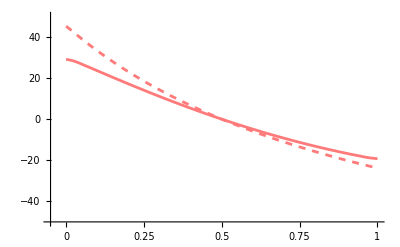

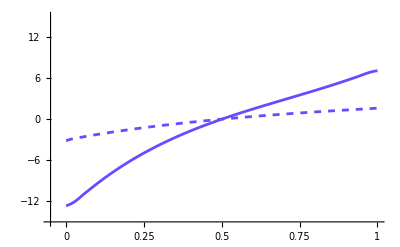

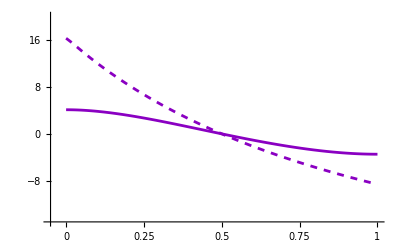

```mathematica
redColor = RGBColor["#ff7a7a"];
blueColor = RGBColor["#654cff"];
purpleColor = RGBColor["#8a00c2"];
betapf = 10;
gammapf = 1;
sigmapf = 1;
mupf = 2000;
grad = 1;
bg = 1;
umax = 10^6;
lcell = 20;
pfd1= Profile[betapf,gammapf/10000,sigmapf,bg*grad/20,bg,mupf,umax,lcell];
pfp1t = Plot[((pfd1[[1]][l]+pfd1[[2]][l])-(pfd1[[1]][.5]+pfd1[[2]][.5]))/(pfd1[[1]][.5]+pfd1[[2]][.5])*100,{l,0,1},PlotStyle->{purpleColor,Dashed},PlotRange->All];
pfp1b = Plot[(pfd1[[2]][l]-pfd1[[2]][.5])/pfd1[[2]][.5]*100,{l,0,1},PlotStyle->{blueColor,Dashed},PlotRange->All];
pfp1r = Plot[(pfd1[[1]][l]-pfd1[[1]][.5])/pfd1[[1]][.5]*100,{l,0,1},PlotStyle->{redColor,Dashed},PlotRange->All];
pfd2= Profile[betapf,gammapf,sigmapf,bg*grad/20,bg,mupf,umax,lcell];
pfp2t = Plot[((pfd2[[1]][l]+pfd2[[2]][l])-(pfd2[[1]][.5]+pfd2[[2]][.5]))/(pfd2[[1]][.5]+pfd2[[2]][.5])*100,{l,0,1},PlotStyle->purpleColor,PlotRange->All];
pfp2b = Plot[(pfd2[[2]][l]-pfd2[[2]][.5])/pfd2[[2]][.5]*100,{l,0,1},PlotStyle->blueColor,PlotRange->All];
pfp2r = Plot[(pfd2[[1]][l]-pfd2[[1]][.5])/pfd2[[1]][.5]*100,{l,0,1},PlotStyle->redColor,PlotRange->All];
(*theory = Plot[(u00+l*u00*g*20)*mu/(beta+beta*((u00+l*u00*g*20)*mu)+mu),{l,0,1},PlotStyle->{Gray,Dashed}];
theory2 = Plot[(beta+mu)/(beta+beta*((u00+l*u00*g*20)*mu)+mu),{l,0,1},PlotStyle->{Gray,Dashed}];*)
pfr = Show[{pfp2r,pfp1r},AxesOrigin->{-0.05,-50},PlotRange->{{-0.05,1},{-50,50}},Ticks->{{0,0.25,0.5,0.75,1},All}]
pfb = Show[{pfp2b,pfp1b},AxesOrigin->{-0.05,-15},PlotRange->{{-0.05,1},{-15,15}},PlotRange->All,Ticks->{{0,0.25,0.5,0.75,1},All}]
pft = Show[{pfp2t,pfp1t},AxesOrigin->{-0.05,-15},PlotRange->{{-0.05,1},{-15,20}},PlotRange->All,Ticks->{{0,0.25,0.5,0.75,1},All}]
Export[fileLocation<>"/r_profile.eps",pfr,"EPS"];
Export[fileLocation<>"/b_profile.eps",pfb,"EPS"];
Export[fileLocation<>"/t_profile.eps",pft,"EPS"];
```

### Sigma vs Gamma heatmap

```mathematica
sgdsg1 = Quiet[ParallelTable[IntBestUdifference[beta,10^gamma,10^-ara,mu,10^7,20,.1,1,"None"],{ara,0,1,.1},{gamma,-1,1,.1}]];
sgdsg1lowg = Quiet[ParallelTable[IntBestUdifference[beta,10^-5,10^-ara,mu,10^7,20,.1,1,"None"],{ara,0,1,.1}]];
sgdsg1relative = sgdsg1/sgdsg1lowg;
```

```mathematica
sgdsg2 = Quiet[ParallelTable[IntBestUdifference[beta,10^gamma,10^-ara,10^7,10^7,20,.1,1,"None"],{ara,0,1,.1},{gamma,-1,1,.1}]];
sgdsg2lowg = Quiet[ParallelTable[IntBestUdifference[beta,10^-5,10^-ara,10^7,10^7,20,.1,1,"None"],{ara,0,1,.1}]];
sgdsg2relative = sgdsg2/sgdsg2lowg;
```

```mathematica
sgdsg3 = Quiet[ParallelTable[IntBestUdifferenceAnalytical[beta,10^gamma*4,10^-ara,.1],{ara,0,1,.1},{gamma,-1,1,.1}]];
sgdsg3lowg = Quiet[ParallelTable[IntBestUdifferenceAnalytical[beta,10^-5*4,10^-ara,.1],{ara,0,1,.1}]];
sgdsg3relative = sgdsg3/sgdsg3lowg;
```

```mathematica
Export[fileLocation<>"/sigma_v_gamma.mx",sgdsg1relative];
Export[fileLocation<>"/sigma_v_gamma_infMu.mx",sgdsg2relative];
Export[fileLocation<>"/sigma_v_gamma_analytical.mx",sgdsg3relative];
```

```mathematica
sgdsg1relative = Import[fileLocation<>"/sigma_v_gamma.mx"];
sgdsg2relative = Import[fileLocation<>"/sigma_v_gamma_infMu.mx"];
sgdsg3relative = Import[fileLocation<>"/sigma_v_gamma_analytical.mx"];
```

```mathematica
sghmsg1 = ListContourPlot[sgdsg1relative,ColorFunction->(ColorData["LightTemperatureMap",Rescale[#,{Min[sgdsg1relative],Max[sgdsg1relative]}]]&),ColorFunctionScaling->False,PlotLegends->BarLegend[{Automatic,{Min[sgdsg1relative],Max[sgdsg1relative]}}],PlotRange->{Min[sgdsg1relative],Max[sgdsg1relative]},DataRange->{{-1,1},{0,1}},Frame->None,Axes -> True,AxesOrigin->{-1.2,-.05},Ticks->{{-1, 0,1}, {0,0.5,1}}];
sghmsg2 = ListContourPlot[sgdsg2relative,ColorFunction->(ColorData["LightTemperatureMap",Rescale[#,{Min[sgdsg3relative,sgdsg2relative],Max[sgdsg3relative,sgdsg2relative]}]]&),ColorFunctionScaling->False,PlotLegends->BarLegend[{Automatic,{Min[sgdsg3relative,sgdsg2relative],Max[sgdsg3relative,sgdsg2relative]}}],PlotRange->{Min[sgdsg3relative,sgdsg2relative],Max[sgdsg3relative,sgdsg2relative]},DataRange->{{-1,1},{0,1}},Frame->None,Axes -> True,AxesOrigin->{-1.2,-.05},Ticks->{{-1, 0,1}, {0,0.5,1}}];
sghmsg3 = ListContourPlot[sgdsg3relative,ColorFunction->(ColorData["LightTemperatureMap",Rescale[#,{Min[sgdsg3relative,sgdsg2relative],Max[sgdsg3relative,sgdsg2relative]}]]&),ColorFunctionScaling->False,PlotLegends->BarLegend[{Automatic,{Min[sgdsg3relative,sgdsg2relative],Max[sgdsg3relative,sgdsg2relative]}}],PlotRange->{Min[sgdsg3relative,sgdsg2relative],Max[sgdsg3relative,sgdsg2relative]},DataRange->{{-1,1},{0,1}},Frame->None,Axes -> True,AxesOrigin->{-1.2,-.05},Ticks->{{-1, 0,1}, {0,0.5,1}}];
```

```mathematica
Export[fileLocation<>"/sigma_v_gamma.eps",sghmsg1,"EPS"];
Export[fileLocation<>"/sigma_v_gamma_infMu.eps",sghmsg2,"EPS"];
Export[fileLocation<>"/sigma_v_gamma_analytical.eps",sghmsg3,"EPS"];
```

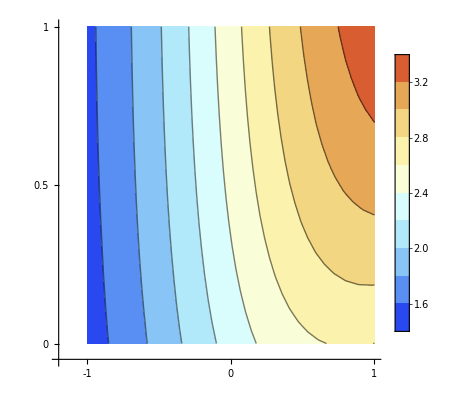

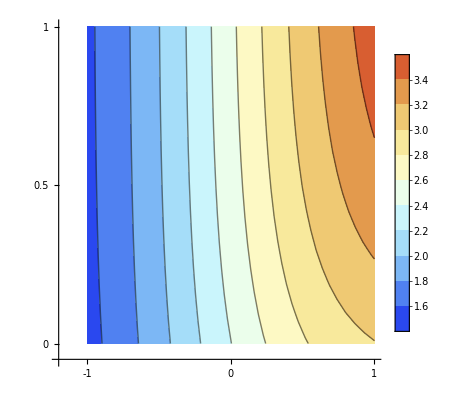

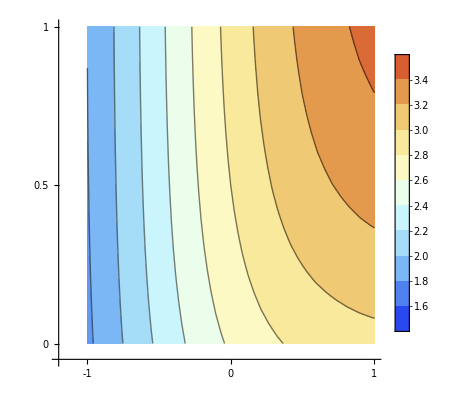

```mathematica
sghmsg1
sghmsg2
sghmsg3
```

### Beta vs Gamma

```mathematica
bgdsg1 = Quiet[ParallelTable[IntBestUdifference[2^beta,10^gamma,1,mu,10^7,20,.1,1,"None"],{beta,0,6,1},{gamma,-1,1,.1}]];
bgdsg2 = Quiet[ParallelTable[IntBestUdifference[2^beta,10^gamma,1,10^7,10^7,20,.1,1,"None"],{beta,0,6,1},{gamma,-1,1,.1}]];
```

```mathematica
bgdsg1lhs = Quiet[ParallelTable[IntBestUdifference[2^beta,10^gamma,1,mu,10^7,20,.1,1,"None"],{beta,0,6,1},{gamma,-5,-4.5,.1}]];
bgdsg2lhs  = Quiet[ParallelTable[IntBestUdifference[2^beta,10^gamma,1,10^7,10^7,20,.1,1,"None"],{beta,0,6,1},{gamma,-5,-4.5,.1}]];
```

```mathematica
bgdsg3 = Quiet[ParallelTable[IntBestUdifferenceAnalytical[2^beta,10^gamma*4,1,.1],{beta,0,6,1},{gamma,-1,1,.1}]];
bgdsg3lhs = Quiet[ParallelTable[IntBestUdifferenceAnalytical[2^beta,10^gamma*4,1,.1],{beta,0,6,1},{gamma,-5,-4.5,.1}]];
```

```mathematica
Export[fileLocation<>"/beta_v_gamma_rhs.mx",bgdsg1];
Export[fileLocation<>"/beta_v_gamma_infMu_rhs.mx",bgdsg2];
Export[fileLocation<>"/beta_v_gamma_analytical_rhs.mx",bgdsg3];
Export[fileLocation<>"/beta_v_gamma_lhs.mx",bgdsg1lhs];
Export[fileLocation<>"/beta_v_gamma_infMu_lhs.mx",bgdsg2lhs];
Export[fileLocation<>"/beta_v_gamma_analytical_lhs.mx",bgdsg3lhs];
```

```mathematica
bgdsg1 = Import[fileLocation<>"/beta_v_gamma_rhs.mx"];
bgdsg2 = Import[fileLocation<>"/beta_v_gamma_infMu_rhs.mx"];
(*bgdsg3 = Import[fileLocation<>"/beta_v_gamma_analytical_rhs.mx"];*)
bgdsg1lhs = Import[fileLocation<>"/beta_v_gamma_lhs.mx"];
bgdsg2lhs = Import[fileLocation<>"/beta_v_gamma_infMu_lhs.mx"];
(*bgdsg3lhs = Import[fileLocation<>"/beta_v_gamma_analytical_lhs.mx"];*)
```

```mathematica
rhsPoints11= Transpose[{Range[-1,1,.1],bgdsg1[[1]]/bgdsg1lhs[[1]][[1]]}];
rhsPoints12= Transpose[{Range[-1,1,.1],bgdsg1[[2]]/bgdsg1lhs[[2]][[1]]}];
rhsPoints13= Transpose[{Range[-1,1,.1],bgdsg1[[3]]/bgdsg1lhs[[3]][[1]]}];
rhsPoints14= Transpose[{Range[-1,1,.1],bgdsg1[[4]]/bgdsg1lhs[[4]][[1]]}];
rhsPoints15= Transpose[{Range[-1,1,.1],bgdsg1[[5]]/bgdsg1lhs[[5]][[1]]}];
rhsPoints16= Transpose[{Range[-1,1,.1],bgdsg1[[6]]/bgdsg1lhs[[6]][[1]]}];
rhsPoints17= Transpose[{Range[-1,1,.1],bgdsg1[[7]]/bgdsg1lhs[[7]][[1]]}];

lhsPoints11= Transpose[{Range[-2,-1.5,.1],bgdsg1lhs[[1]]/bgdsg1lhs[[1]][[1]]}];
lhsPoints12= Transpose[{Range[-2,-1.5,.1],bgdsg1lhs[[2]]/bgdsg1lhs[[2]][[1]]}];
lhsPoints13= Transpose[{Range[-2,-1.5,.1],bgdsg1lhs[[3]]/bgdsg1lhs[[3]][[1]]}];
lhsPoints14= Transpose[{Range[-2,-1.5,.1],bgdsg1lhs[[4]]/bgdsg1lhs[[4]][[1]]}];
lhsPoints15= Transpose[{Range[-2,-1.5,.1],bgdsg1lhs[[5]]/bgdsg1lhs[[5]][[1]]}];
lhsPoints16= Transpose[{Range[-2,-1.5,.1],bgdsg1lhs[[6]]/bgdsg1lhs[[6]][[1]]}];
lhsPoints17= Transpose[{Range[-2,-1.5,.1],bgdsg1lhs[[7]]/bgdsg1lhs[[7]][[1]]}];

mPoints11 = {lhsPoints11[[-1]],rhsPoints11[[1]]};
mPoints12 = {lhsPoints12[[-1]],rhsPoints12[[1]]};
mPoints13 = {lhsPoints13[[-1]],rhsPoints13[[1]]};
mPoints14 = {lhsPoints14[[-1]],rhsPoints14[[1]]};
mPoints15 = {lhsPoints15[[-1]],rhsPoints15[[1]]};
mPoints16 = {lhsPoints16[[-1]],rhsPoints16[[1]]};
mPoints17 = {lhsPoints17[[-1]],rhsPoints17[[1]]};

rhsPoints21= Transpose[{Range[-1,1,.1],bgdsg2[[1]]/bgdsg2lhs[[1]][[1]]}];
rhsPoints22= Transpose[{Range[-1,1,.1],bgdsg2[[2]]/bgdsg2lhs[[2]][[1]]}];
rhsPoints23= Transpose[{Range[-1,1,.1],bgdsg2[[3]]/bgdsg2lhs[[3]][[1]]}];
rhsPoints24= Transpose[{Range[-1,1,.1],bgdsg2[[4]]/bgdsg2lhs[[4]][[1]]}];
rhsPoints25= Transpose[{Range[-1,1,.1],bgdsg2[[5]]/bgdsg2lhs[[5]][[1]]}];
rhsPoints26= Transpose[{Range[-1,1,.1],bgdsg2[[6]]/bgdsg2lhs[[6]][[1]]}];
rhsPoints27= Transpose[{Range[-1,1,.1],bgdsg2[[7]]/bgdsg2lhs[[7]][[1]]}];

lhsPoints21= Transpose[{Range[-2,-1.5,.1],bgdsg2lhs[[1]]/bgdsg2lhs[[1]][[1]]}];
lhsPoints22= Transpose[{Range[-2,-1.5,.1],bgdsg2lhs[[2]]/bgdsg2lhs[[2]][[1]]}];
lhsPoints23= Transpose[{Range[-2,-1.5,.1],bgdsg2lhs[[3]]/bgdsg2lhs[[3]][[1]]}];
lhsPoints24= Transpose[{Range[-2,-1.5,.1],bgdsg2lhs[[4]]/bgdsg2lhs[[4]][[1]]}];
lhsPoints25= Transpose[{Range[-2,-1.5,.1],bgdsg2lhs[[5]]/bgdsg2lhs[[5]][[1]]}];
lhsPoints26= Transpose[{Range[-2,-1.5,.1],bgdsg2lhs[[6]]/bgdsg2lhs[[6]][[1]]}];
lhsPoints27= Transpose[{Range[-2,-1.5,.1],bgdsg2lhs[[7]]/bgdsg2lhs[[7]][[1]]}];

mPoints21 = {lhsPoints21[[-1]],rhsPoints21[[1]]};
mPoints22 = {lhsPoints22[[-1]],rhsPoints22[[1]]};
mPoints23 = {lhsPoints23[[-1]],rhsPoints23[[1]]};
mPoints24 = {lhsPoints24[[-1]],rhsPoints24[[1]]};
mPoints25 = {lhsPoints25[[-1]],rhsPoints25[[1]]};
mPoints26 = {lhsPoints26[[-1]],rhsPoints26[[1]]};
mPoints27 = {lhsPoints27[[-1]],rhsPoints27[[1]]};

rhsPoints31= Transpose[{Range[-1,1,.1],bgdsg3[[1]]/bgdsg3lhs[[1]][[1]]}];
rhsPoints32= Transpose[{Range[-1,1,.1],bgdsg3[[2]]/bgdsg3lhs[[2]][[1]]}];
rhsPoints33= Transpose[{Range[-1,1,.1],bgdsg3[[3]]/bgdsg3lhs[[3]][[1]]}];
rhsPoints34= Transpose[{Range[-1,1,.1],bgdsg3[[4]]/bgdsg3lhs[[4]][[1]]}];
rhsPoints35= Transpose[{Range[-1,1,.1],bgdsg3[[5]]/bgdsg3lhs[[5]][[1]]}];
rhsPoints36= Transpose[{Range[-1,1,.1],bgdsg3[[6]]/bgdsg3lhs[[6]][[1]]}];
rhsPoints37= Transpose[{Range[-1,1,.1],bgdsg3[[7]]/bgdsg3lhs[[7]][[1]]}];

lhsPoints31= Transpose[{Range[-2,-1.5,.1],bgdsg3lhs[[1]]/bgdsg3lhs[[1]][[1]]}];
lhsPoints32= Transpose[{Range[-2,-1.5,.1],bgdsg3lhs[[2]]/bgdsg3lhs[[2]][[1]]}];
lhsPoints33= Transpose[{Range[-2,-1.5,.1],bgdsg3lhs[[3]]/bgdsg3lhs[[3]][[1]]}];
lhsPoints34= Transpose[{Range[-2,-1.5,.1],bgdsg3lhs[[4]]/bgdsg3lhs[[4]][[1]]}];
lhsPoints35= Transpose[{Range[-2,-1.5,.1],bgdsg3lhs[[5]]/bgdsg3lhs[[5]][[1]]}];
lhsPoints36= Transpose[{Range[-2,-1.5,.1],bgdsg3lhs[[6]]/bgdsg3lhs[[6]][[1]]}];
lhsPoints37= Transpose[{Range[-2,-1.5,.1],bgdsg3lhs[[7]]/bgdsg3lhs[[7]][[1]]}];

mPoints31 = {lhsPoints31[[-1]],rhsPoints31[[1]]};
mPoints32 = {lhsPoints32[[-1]],rhsPoints32[[1]]};
mPoints33 = {lhsPoints33[[-1]],rhsPoints33[[1]]};
mPoints34 = {lhsPoints34[[-1]],rhsPoints34[[1]]};
mPoints35 = {lhsPoints35[[-1]],rhsPoints35[[1]]};
mPoints36 = {lhsPoints36[[-1]],rhsPoints36[[1]]};
mPoints37 = {lhsPoints37[[-1]],rhsPoints37[[1]]};
```

```mathematica
thickness = 0.008;
color = RGBColor["#00F9A4"];
bgp11 = ListLinePlot[rhsPoints11,PlotStyle->{color,Opacity[.2],Thickness[thickness]},PlotRange->All];
bgp12 = ListLinePlot[rhsPoints12,PlotStyle-> {color,Opacity[.3],Thickness[thickness]},PlotRange->All];
bgp13 = ListLinePlot[rhsPoints13,PlotStyle-> {color,Opacity[.4],Thickness[thickness]},PlotRange->All];
bgp14 = ListLinePlot[rhsPoints14,PlotStyle->{color,Opacity[.5],Thickness[thickness]},PlotRange->All];
bgp15 = ListLinePlot[rhsPoints15,PlotStyle->{color,Opacity[.6],Thickness[thickness]},PlotRange->All];
bgp16 = ListLinePlot[rhsPoints16,PlotStyle->{color,Opacity[.8],Thickness[thickness]},PlotRange->All];
bgp17 = ListLinePlot[rhsPoints17,PlotStyle-> {color,Opacity[1],Thickness[thickness]},PlotRange->All];

bgp11lhs = ListLinePlot[lhsPoints11,PlotStyle->{color,Opacity[.2],Thickness[thickness]},PlotRange->All];
bgp12lhs = ListLinePlot[lhsPoints12,PlotStyle->{color,Opacity[.3],Thickness[thickness]},PlotRange->All];
bgp13lhs = ListLinePlot[lhsPoints13,PlotStyle->{color,Opacity[.4],Thickness[thickness]},PlotRange->All];
bgp14lhs = ListLinePlot[lhsPoints14,PlotStyle->{color,Opacity[.5],Thickness[thickness]},PlotRange->All];
bgp15lhs = ListLinePlot[lhsPoints15,PlotStyle->{color,Opacity[.6],Thickness[thickness]},PlotRange->All];
bgp16lhs = ListLinePlot[lhsPoints16,PlotStyle->{color,Opacity[.8],Thickness[thickness]},PlotRange->All];
bgp17lhs = ListLinePlot[lhsPoints17,PlotStyle->{color,Opacity[1],Thickness[thickness]},PlotRange->All];

bgp11m= ListLinePlot[mPoints11,PlotStyle->{color,Opacity[.2],Dashed,Thickness[thickness]},PlotRange->All];
bgp12m= ListLinePlot[mPoints12,PlotStyle->{color,Opacity[.3],Dashed,Thickness[thickness]},PlotRange->All];
bgp13m= ListLinePlot[mPoints13,PlotStyle->{color,Opacity[.4],Dashed,Thickness[thickness]},PlotRange->All];
bgp14m= ListLinePlot[mPoints14,PlotStyle->{color,Opacity[.5],Dashed,Thickness[thickness]},PlotRange->All];
bgp15m= ListLinePlot[mPoints15,PlotStyle->{color,Opacity[.6],Dashed,Thickness[thickness]},PlotRange->All];
bgp16m= ListLinePlot[mPoints16,PlotStyle->{color,Opacity[.8],Dashed,Thickness[thickness]},PlotRange->All];
bgp17m= ListLinePlot[mPoints17,PlotStyle->{color,Opacity[1],Dashed,Thickness[thickness]},PlotRange->All];

bgp21 = ListLinePlot[rhsPoints21,PlotStyle->{color,Opacity[.2],Thickness[thickness]},PlotRange->All];
bgp22 = ListLinePlot[rhsPoints22,PlotStyle->{color,Opacity[.3],Thickness[thickness]},PlotRange->All];
bgp23 = ListLinePlot[rhsPoints23,PlotStyle->{color,Opacity[.4],Thickness[thickness]},PlotRange->All];
bgp24 = ListLinePlot[rhsPoints24,PlotStyle->{color,Opacity[.5],Thickness[thickness]},PlotRange->All];
bgp25 = ListLinePlot[rhsPoints25,PlotStyle->{color,Opacity[.6],Thickness[thickness]},PlotRange->All];
bgp26 = ListLinePlot[rhsPoints26,PlotStyle->{color,Opacity[.8],Thickness[thickness]},PlotRange->All];
bgp27 = ListLinePlot[rhsPoints27,PlotStyle->{color,Opacity[1],Thickness[thickness]},PlotRange->All];

bgp21lhs = ListLinePlot[lhsPoints21,PlotStyle->{color,Opacity[.2],Thickness[thickness]},PlotRange->All];
bgp22lhs = ListLinePlot[lhsPoints22,PlotStyle->{color,Opacity[.3],Thickness[thickness]},PlotRange->All];
bgp23lhs = ListLinePlot[lhsPoints23,PlotStyle->{color,Opacity[.4],Thickness[thickness]},PlotRange->All];
bgp24lhs = ListLinePlot[lhsPoints24,PlotStyle->{color,Opacity[.5],Thickness[thickness]},PlotRange->All];
bgp25lhs = ListLinePlot[lhsPoints25,PlotStyle->{color,Opacity[.6],Thickness[thickness]},PlotRange->All];
bgp26lhs = ListLinePlot[lhsPoints26,PlotStyle->{color,Opacity[.8],Thickness[thickness]},PlotRange->All];
bgp27lhs = ListLinePlot[lhsPoints27,PlotStyle->{color,Opacity[1],Thickness[thickness]},PlotRange->All];

bgp21m= ListLinePlot[mPoints21,PlotStyle->{color,Opacity[.2],Dashed,Thickness[thickness]},PlotRange->All];
bgp22m= ListLinePlot[mPoints22,PlotStyle->{color,Opacity[.3],Dashed,Thickness[thickness]},PlotRange->All];
bgp23m= ListLinePlot[mPoints23,PlotStyle->{color,Opacity[.4],Dashed,Thickness[thickness]},PlotRange->All];
bgp24m= ListLinePlot[mPoints24,PlotStyle->{color,Opacity[.5],Dashed,Thickness[thickness]},PlotRange->All];
bgp25m= ListLinePlot[mPoints25,PlotStyle->{color,Opacity[.6],Dashed,Thickness[thickness]},PlotRange->All];
bgp26m= ListLinePlot[mPoints26,PlotStyle->{color,Opacity[.8],Dashed,Thickness[thickness]},PlotRange->All];
bgp27m= ListLinePlot[mPoints27,PlotStyle->{color,Opacity[1],Dashed,Thickness[thickness]},PlotRange->All];

bgp31 = ListLinePlot[rhsPoints31,PlotStyle->{color,Opacity[.2],Thickness[thickness]},PlotRange->All];
bgp32 = ListLinePlot[rhsPoints32,PlotStyle->{color,Opacity[.3],Thickness[thickness]},PlotRange->All];
bgp33 = ListLinePlot[rhsPoints33,PlotStyle->{color,Opacity[.4],Thickness[thickness]},PlotRange->All];
bgp34 = ListLinePlot[rhsPoints34,PlotStyle->{color,Opacity[.5],Thickness[thickness]},PlotRange->All];
bgp35 = ListLinePlot[rhsPoints35,PlotStyle->{color,Opacity[.6],Thickness[thickness]},PlotRange->All];
bgp36 = ListLinePlot[rhsPoints36,PlotStyle->{color,Opacity[.8],Thickness[thickness]},PlotRange->All];
bgp37 = ListLinePlot[rhsPoints37,PlotStyle->{color,Opacity[1],Thickness[thickness]},PlotRange->All];

bgp31lhs = ListLinePlot[lhsPoints21,PlotStyle->{color,Opacity[.2],Thickness[thickness]},PlotRange->All];
bgp32lhs = ListLinePlot[lhsPoints22,PlotStyle->{color,Opacity[.3],Thickness[thickness]},PlotRange->All];
bgp33lhs = ListLinePlot[lhsPoints23,PlotStyle->{color,Opacity[.4],Thickness[thickness]},PlotRange->All];
bgp34lhs = ListLinePlot[lhsPoints24,PlotStyle->{color,Opacity[.5],Thickness[thickness]},PlotRange->All];
bgp35lhs = ListLinePlot[lhsPoints25,PlotStyle->{color,Opacity[.6],Thickness[thickness]},PlotRange->All];
bgp36lhs = ListLinePlot[lhsPoints26,PlotStyle->{color,Opacity[.8],Thickness[thickness]},PlotRange->All];
bgp37lhs = ListLinePlot[lhsPoints27,PlotStyle->{color,Opacity[1],Thickness[thickness]},PlotRange->All];

bgp31m= ListLinePlot[mPoints31,PlotStyle->{color,Opacity[.2],Dashed,Thickness[thickness]},PlotRange->All];
bgp32m= ListLinePlot[mPoints32,PlotStyle->{color,Opacity[.3],Dashed,Thickness[thickness]},PlotRange->All];
bgp33m= ListLinePlot[mPoints33,PlotStyle->{color,Opacity[.4],Dashed,Thickness[thickness]},PlotRange->All];
bgp34m= ListLinePlot[mPoints34,PlotStyle->{color,Opacity[.5],Dashed,Thickness[thickness]},PlotRange->All];
bgp35m= ListLinePlot[mPoints35,PlotStyle->{color,Opacity[.6],Dashed,Thickness[thickness]},PlotRange->All];
bgp36m= ListLinePlot[mPoints36,PlotStyle->{color,Opacity[.8],Dashed,Thickness[thickness]},PlotRange->All];
bgp37m= ListLinePlot[mPoints37,PlotStyle->{color,Opacity[1],Dashed,Thickness[thickness]},PlotRange->All];
```

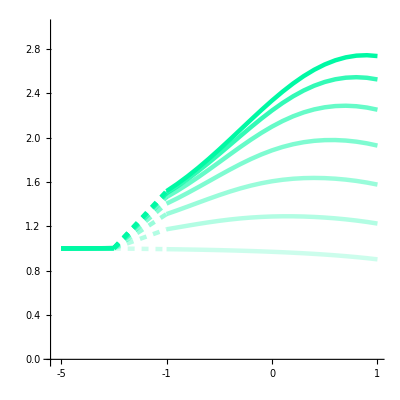

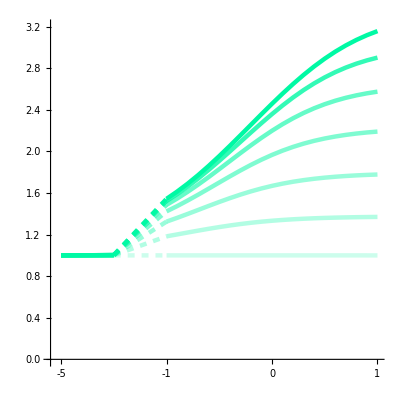

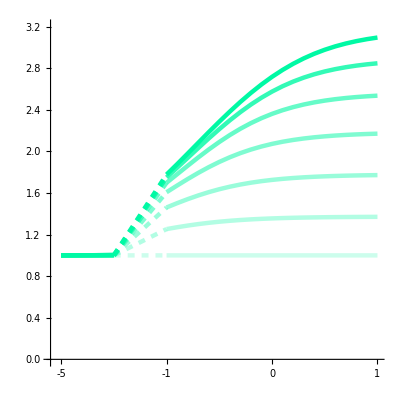

```mathematica
tickMarks = {{-2,-5},{-1.5,-4.5},{-1,-1},{-.5,-.5},{0,0},{.5,.5},{1,1}};
bgfp = Show[{bgp11,bgp12,bgp13,bgp14,bgp15,bgp16,bgp17,bgp11lhs,bgp12lhs,bgp13lhs,bgp14lhs,bgp15lhs,bgp16lhs,bgp17lhs,bgp11m,bgp12m,bgp13m,bgp14m,bgp15m,bgp16m,bgp17m},Ticks->{tickMarks, Automatic},AxesOrigin->{-2.1,0},PlotRange->{{-2.1,1},{0,3}},AspectRatio->1]
bgfpim = Show[{bgp21,bgp22,bgp23,bgp24,bgp25,bgp26,bgp27,bgp21lhs,bgp22lhs,bgp23lhs,bgp24lhs,bgp25lhs,bgp26lhs,bgp27lhs,bgp21m,bgp22m,bgp23m,bgp24m,bgp25m,bgp26m,bgp27m},Ticks->{tickMarks, Automatic},AxesOrigin->{-2.1,0},PlotRange->{{-2.1,1},{0,3.2}},AspectRatio->1]
bgfpan = Show[{bgp31,bgp32,bgp33,bgp34,bgp35,bgp36,bgp37,bgp31lhs,bgp32lhs,bgp33lhs,bgp34lhs,bgp35lhs,bgp36lhs,bgp37lhs,bgp31m,bgp32m,bgp33m,bgp34m,bgp35m,bgp36m,bgp37m},Ticks->{tickMarks, Automatic},AxesOrigin->{-2.1,0},PlotRange->{{-2.1,1},{0,3.2}},AspectRatio->1]
Export[fileLocation<>"/performance_v_gamma.eps",bgfp,"EPS"];
Export[fileLocation<>"/performance_v_gamma_infmu.eps",bgfpim,"EPS"];
Export[fileLocation<>"/performance_v_gamma_ana.eps",bgfpan,"EPS"];
```

### Performance vs sigma for different beta values

```mathematica
bst1 = ParallelTable[IntBestUdifference[2^beta,gamma,10^-ara,mu,10^7,20,.1,1,"None"],{beta,0,6,1},{ara,0,1,0.1}];
bst1minara = ParallelTable[IntBestUdifference[2^beta,gamma,1,mu,10^7,20,.1,1,"None"],{beta,0,6,1}];
relbst1 = bst1/bst1minara;
bst2 = ParallelTable[IntBestUdifference[2^beta,gamma,10^-ara,10^7,10^7,20,.1,1,"None"],{beta,0,6,1},{ara,0,1,0.1}];
bst2minara = ParallelTable[IntBestUdifference[2^beta,gamma,1,10^7,10^7,20,.1,1,"None"],{beta,0,6,1}];
relbst2 = bst2/bst2minara;
```

```mathematica
bst3 = ParallelTable[IntBestUdifferenceAnalytical[2^beta,gamma*4,10^-ara,.1],{beta,0,6,1},{ara,0,1,0.1}];
bst3minara = ParallelTable[IntBestUdifferenceAnalytical[2^beta,gamma*4,1,.1],{beta,0,6,1}];
relbst3 = bst3/bst3minara;
```

```mathematica
Export[fileLocation<>"/sigma_v_beta.mx",relbst1];
Export[fileLocation<>"/sigma_v_beta_infMu.mx",relbst2];
Export[fileLocation<>"/sigma_v_beta_analytical.mx",relbst3];
```

```mathematica
relbst1 = Import[fileLocation<>"/sigma_v_beta.mx"];
relbst2 = Import[fileLocation<>"/sigma_v_beta_infMu.mx"];
relbst3 = Import[fileLocation<>"/sigma_v_beta_analytical.mx"];
```

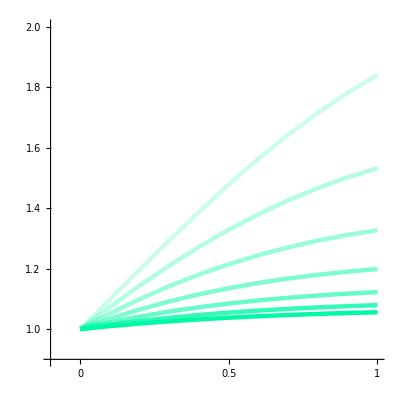

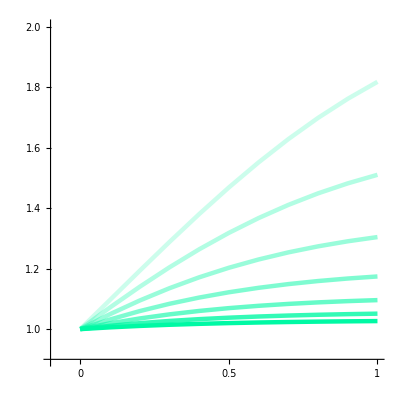

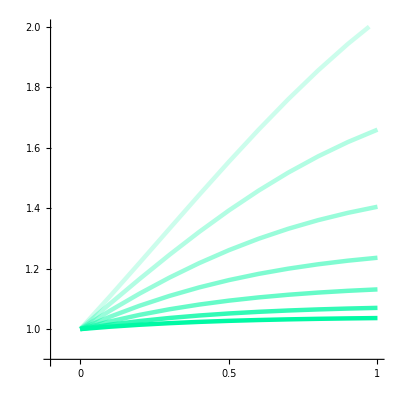

```mathematica
thickness = 0.008;
color = RGBColor["#00F9A4"];
bslp1 = ListLinePlot[relbst1,PlotRange->{{0,11},{0.9,2}},AxesOrigin->{0,0.9},Ticks->{{{1,0},{6,0.5},{11,1}},All},PlotStyle->{{color,Opacity[.2],Thickness[thickness]},{color,Opacity[.3],Thickness[thickness]},{color,Opacity[.4],Thickness[thickness]},{color,Opacity[.5],Thickness[thickness]},{color,Opacity[.6],Thickness[thickness]},{color,Opacity[.8],Thickness[thickness]},{color,Opacity[1],Thickness[thickness]}},AspectRatio->1]
bslp2 = ListLinePlot[relbst2,PlotRange->{{0,11},{0.9,2}},AxesOrigin->{0,0.9},Ticks->{{{1,0},{6,0.5},{11,1}},All},PlotStyle->{{RGBColor["#00F9A4"],Opacity[.2],Thickness[thickness]},{RGBColor["#00F9A4"],Opacity[.3],Thickness[thickness]},{RGBColor["#00F9A4"],Opacity[.4],Thickness[thickness]},{RGBColor["#00F9A4"],Opacity[.5],Thickness[thickness]},{RGBColor["#00F9A4"],Opacity[.6],Thickness[thickness]},{RGBColor["#00F9A4"],Opacity[.8],Thickness[thickness]},{RGBColor["#00F9A4"],Opacity[1],Thickness[thickness]}},AspectRatio->1]
bslp3 = ListLinePlot[relbst3,PlotRange->{{0,11},{0.9,2}},AxesOrigin->{0,0.9},Ticks->{{{1,0},{6,0.5},{11,1}},All},PlotStyle->{{RGBColor["#00F9A4"],Opacity[.2],Thickness[thickness]},{RGBColor["#00F9A4"],Opacity[.3],Thickness[thickness]},{RGBColor["#00F9A4"],Opacity[.4],Thickness[thickness]},{RGBColor["#00F9A4"],Opacity[.5],Thickness[thickness]},{RGBColor["#00F9A4"],Opacity[.6],Thickness[thickness]},{RGBColor["#00F9A4"],Opacity[.8],Thickness[thickness]},{RGBColor["#00F9A4"],Opacity[1],Thickness[thickness]}},AspectRatio->1]
Export[fileLocation<>"/beta_v_sigma_color.eps",bslp1,"EPS"];
Export[fileLocation<>"/beta_v_sigma_color_infmu.eps",bslp2,"EPS"];
Export[fileLocation<>"/beta_v_sigma_color_ana.eps",bslp3,"EPS"];
```

### Mu vs Gamma

```mathematica
mg3 = Quiet[ParallelTable[IntBestUdifference[beta,10^gamma,1,10^mu,10^7,20,.1,1,"Max"],{mu,0,3,.1},{gamma,-1,1,.1}]];
mg3lowg = Quiet[ParallelTable[IntBestUdifference[beta,10^-5,1,10^mu,10^7,20,.1,1,"Max"],{mu,0,3,.1}]];
mg3rel = mg3/mg3lowg;
```

```mathematica
Export[fileLocation<>"/mu_v_gamma.mx",mg3rel];
```

```mathematica
mg3rel = Import[fileLocation<>"/mu_v_gamma.mx"];
```

```mathematica
mgp3 = ListContourPlot[mg3rel,ColorFunction->(ColorData["LightTemperatureMap",Rescale[#,{Min[mg3rel],Max[mg3rel]}]]&),ColorFunctionScaling->False,PlotLegends->BarLegend[{Automatic,{Min[mg3rel],Max[mg3rel]}}],PlotRange->{Min[mg3rel],Max[mg3rel]},DataRange->{{-1,1},{0,3}},Frame->None,Axes -> True,AxesOrigin->{-1.2,-.1},Ticks->{{-1, 0,1}, {0,1,2,3}}];
```

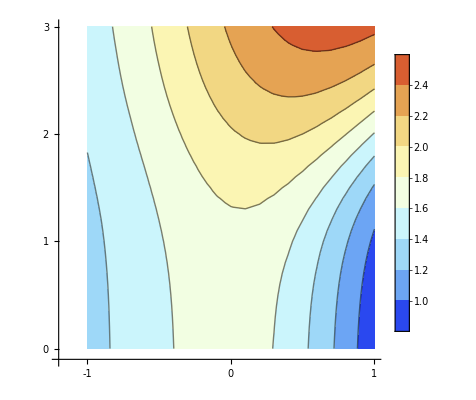

```mathematica
Export[fileLocation<>"/mu_v_gamma_10_large_range.eps",mgp3,"EPS"];
mgp3
```

### Mu vs Sigma

```mathematica
ms1 = Quiet[ParallelTable[IntBestUdifference[10,gamma,10^sigma,10^mu,10^6,20,.1,1,"None"],{mu,2,5,.1},{sigma,-1,0,.1}]];
ms2 = Quiet[ParallelTable[IntBestUdifference[1,gamma,10^sigma,10^mu,10^6,20,.1,1,"None"],{mu,2,5,.1},{sigma,-1,0,.1}]];
```

```mathematica
ms1ws = Quiet[ParallelTable[IntBestUdifference[10,10^-5,1,10^mu,10^6,20,.1,1,"None"],{mu,2,5,.1}]];
ms2ws = Quiet[ParallelTable[IntBestUdifference[1,10^-5,1,10^mu,10^6,20,.1,1,"None"],{mu,2,5,.1}]];
ms1s = ms1/ms1ws;
ms2s = ms2/ms2ws;
```

```mathematica
msp1 = ListContourPlot[ms1s,ColorFunction->(ColorData["LightTemperatureMap",Rescale[#,{Min[ms1s],Max[ms1s]}]]&),ColorFunctionScaling->False,PlotLegends->BarLegend[{Automatic,{Min[ms1s],Max[ms1s]}}],PlotRange->{Min[ms1s],Max[ms1s]},DataRange->{{-1,2},{2,5}},Frame->None,Axes -> True,AxesOrigin->{-1.1,1.8},Ticks->{{-1,0,1,2},{2, 3,4,5}}];
msp2 = ListContourPlot[ms2s,ColorFunction->(ColorData["LightTemperatureMap",Rescale[#,{Min[ms2s],Max[ms2s]}]]&),ColorFunctionScaling->False,PlotLegends->BarLegend[{Automatic,{Min[ms2s],Max[ms2s]}}],PlotRange->{Min[ms2s],Max[ms2s]},DataRange->{{-1,2},{2,5}},Frame->None,Axes -> True,AxesOrigin->{-1.1,1.8},Ticks->{{-1,0,1,2},{2, 3,4,5}}];
```

### Relative Sensing Monomer

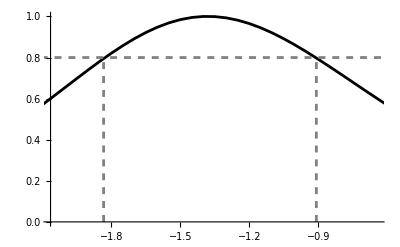

```mathematica
(*dr0,g0,u00,kn10,Lc0,umax,weight,type*)
elrpb1 = Quiet[ParallelTable[singleValue[40,0.1,1,10^u0*0.1/20,10^u0,10^3,10^6,20,"Max","difference"],{u0,-4,2,0.05}]];
elrpb1r = elrpb1/Max[elrpb1];
rangeP1 = Range[-4,2,0.05];
ticklabelsP1 = Range[1,Length[Range[-4,2,0.05]]];
ticks = Transpose[{ticklabelsP1,rangeP1}][[1;;Length[Range[-4,2,0.05]];;1]];
elrpb1points = Transpose[{rangeP1,elrpb1r}];
(*p1 = Select[elrpb1points,#[[2]]>Max[elrpb1]/10&];*)
pl1 = ListLinePlot[elrpb1points,PlotRange->{{-2.065,-0.642},Automatic},AxesOrigin->{-2.065,0},PlotStyle->Black];
pl2 = ListLinePlot[{{-3,.8},{1,.8}},PlotRange->{{-2.065,-0.642},Automatic},AxesOrigin->{-2.065,0},PlotStyle->{Dashed,Gray}];
pl3 = ListLinePlot[{{-1.834,0},{-1.834,.8}},PlotRange->{{-2.065,-0.642},Automatic},AxesOrigin->{-2.065,0},PlotStyle->{Dashed,Gray}];
pl4 = ListLinePlot[{{-.908,0},{-.908,.8}},PlotRange->{{-2.065,-0.642},Automatic},AxesOrigin->{-2.065,0},PlotStyle->{Dashed,Gray}];
(*elrpb5 = 
Quiet[ParallelTable[singleValueNoDeg[0.0001,10^u0*0.1/20,10^u0,1000,20,10^6,"None","RHS"],{u0,-4,-3,0.05}]];*)
(*s5 = ListLinePlot[elrpb5,Ticks->{ticks, Automatic},PlotStyle->Red];*)
sensitiveRange = Show[{pl1,pl2,pl3,pl4}]
Export[fileLocation<>"/sensitive_range.eps",sensitiveRange,"EPS"];
```

### Dimer/monomer sensitive region width

```mathematica
(*This section is extremely slow. It is possible to speed things up by replacing 0.001 with 0.05*)
drpb1 = ParallelTable[Quiet[singleValueDimer[10^beta,0.4,1,10^(0),10^(-1.25+3.6),10^u0*.1/20,10^u0,mu,10^7,20,"None","difference"]],{beta,0,2,0.1},{u0,-4,2,0.001}];
dwrpb1 = drpb1/(Max /@drpb1);
drpb2 = ParallelTable[Quiet[singleValueDimer[10^beta,0.4,1,3,10^(-1.25+3.6),10^u0*.1/20,10^u0,mu,10^7,20,"None","difference"]],{beta,0,2,0.1},{u0,-4,2,0.001}];
dwrpb2 = drpb2/(Max /@drpb2);
drpb3 = ParallelTable[Quiet[singleValueDimer[10^beta,0.4,1,10,10^(-1.25+3.6),10^u0*.1/20,10^u0,mu,10^7,20,"None","difference"]],{beta,0,2,0.1},{u0,-4,2,0.001}];
dwrpb3 = drpb3/(Max /@drpb3);
drpb4 = ParallelTable[Quiet[singleValue[10^beta,0.4,1,10^u0*.1/20,10^u0,mu,10^7,20,"None","difference"]],{beta,0,2,0.1},{u0,-4,2,0.001}];
dwrpb4 = drpb4/(Max /@drpb4);
```

```mathematica
Export[fileLocation<>"/dimer_sense_range_1.mx",dwrpb1];
Export[fileLocation<>"/dimer_sense_range_2.mx",dwrpb2];
Export[fileLocation<>"/dimer_sense_range_3.mx",dwrpb3];
Export[fileLocation<>"/dimer_sense_range_4.mx",dwrpb4];
```

```mathematica
dwrpb1 = Import[fileLocation<>"/dimer_sense_range_1.mx"];
dwrpb2 = Import[fileLocation<>"/dimer_sense_range_2.mx"];
dwrpb3 = Import[fileLocation<>"/dimer_sense_range_3.mx"];
dwrpb4 = Import[fileLocation<>"/dimer_sense_range_4.mx"];
```

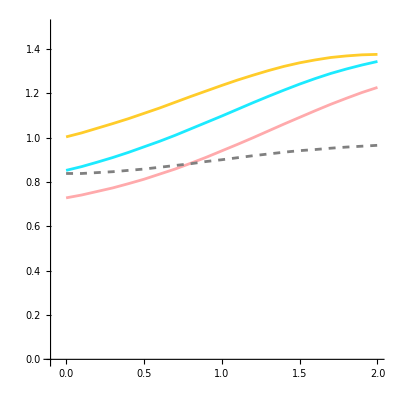

```mathematica
bgc1 = RGBColor["#ff4747"];
bgc2 =  RGBColor["#ffa83f"];
bgc4= RGBColor["#654cff"];

thresh[x_]:=If[x>=0.8,1,0]
betas = Range[0,2,0.1];
ranges1 = Total[Map[thresh,dwrpb1,{2}],{2}]*0.001;
ranges2 = Total[Map[thresh,dwrpb2,{2}],{2}]*0.001;
ranges3 = Total[Map[thresh,dwrpb3,{2}],{2}]*0.001;
ranges4 = Total[Map[thresh,dwrpb4,{2}],{2}]*0.001;
perfRange1 = ListLinePlot[Transpose[{betas,ranges1}],PlotStyle->pRed,AspectRatio->1];
perfRange2 = ListLinePlot[Transpose[{betas,ranges2}],PlotStyle->pBlue,AspectRatio->1];
perfRange3 = ListLinePlot[Transpose[{betas,ranges3}],PlotStyle->pOrange,AspectRatio->1];
perfRange4 = ListLinePlot[Transpose[{betas,ranges4}],PlotStyle->{Dashed,Gray},AspectRatio->1];
sensitiveRanges = Show[{perfRange1,perfRange2,perfRange3,perfRange4},PlotRange->{{-0.1,2},{0,1.5}},AxesOrigin->{-.1,0.0}]
Export[fileLocation<>"/sensitive_ranges.eps",sensitiveRanges,"EPS"];
```

### Fold Change Detection

```mathematica
testb1 = Quiet[ParallelTable[singleValue[1,gamma,1,10^u00*alpha/20,10^u00,mu,10^7,20,"None","difference"],{alpha,0.025,0.1,0.025},{u00,-4,2,.05}]];
testb2 = Quiet[ParallelTable[singleValue[10,gamma,1,10^u00*alpha/20,10^u00,mu,10^7,20,"None","difference"],{alpha,0.025,0.1,0.025},{u00,-4,2,.05}]];
testb3 = Quiet[ParallelTable[singleValue[40,gamma,1,10^u00*alpha/20,10^u00,mu,10^7,20,"None","difference"],{alpha,0.025,0.1,0.025},{u00,-4,2,.05}]];
testb4 = Quiet[ParallelTable[singleValue[100,gamma,1,10^u00*alpha/20,10^u00,mu,10^7,20,"None","difference"],{alpha,0.025,0.1,0.025},{u00,-4,2,.05}]];
```

0.00113977

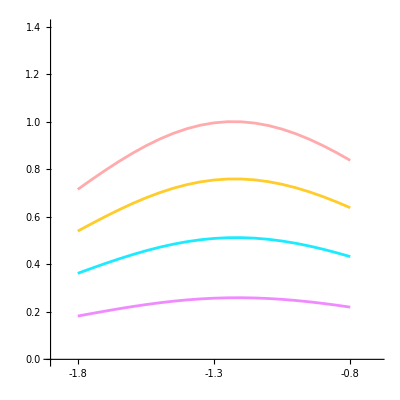

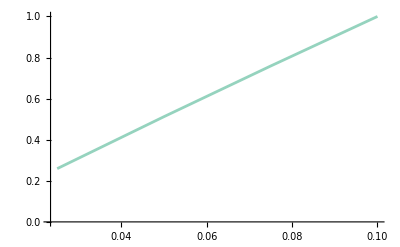

```mathematica
bgc1 = RGBColor["#ff4747"];
bgc2 =  RGBColor["#ffa83f"];
bgc3 = RGBColor["#1ceaff"];
bgc4= RGBColor["#654cff"];

maxfcd = Max[testb3[[4]]]
alpha025 = Transpose[{Array[#&,121,{-4.,2}],testb3[[1]]/maxfcd}][[45;;65]];
alpha05 = Transpose[{Array[#&,121,{-4.,2}],testb3[[2]]/maxfcd}][[45;;65]];
alpha075 = Transpose[{Array[#&,121,{-4.,2}],testb3[[3]]/maxfcd}][[45;;65]];
alpha1 = Transpose[{Array[#&,121,{-4.,2}],testb3[[4]]/maxfcd}][[45;;65]];
palpha025 = ListLinePlot[alpha025,PlotStyle->pPink,AspectRatio->1];
palpha05 = ListLinePlot[alpha05,PlotStyle->pBlue,AspectRatio->1];
palpha075 = ListLinePlot[alpha075,PlotStyle->pOrange,AspectRatio->1];
palpha1 = ListLinePlot[alpha1,PlotStyle->pRed,AspectRatio->1];
FCD = Show[{palpha025,palpha05,palpha075,palpha1},PlotRange->{{-1.90,-0.7},{0,1.4}},AxesOrigin->{-1.9,0},Ticks->{{-1.8,-1.3,-0.8},All},AspectRatio->1]
Export[fileLocation<>"/FCD.eps",FCD,"EPS"];
maxVals = Max /@testb3;
maxVals = maxVals/Max[maxVals];
maxValPoints = Transpose[{Array[#&,4,{0.025,0.1}],maxVals}];
fcdTrend = ListLinePlot[maxValPoints,PlotStyle->pJade]
Export[fileLocation<>"/FCD.eps",FCD,"EPS"];
Export[fileLocation<>"/FCDTrend.eps",fcdTrend,"EPS"];
```

### Animation of performance

```mathematica
(*Generates animation of response profile along the cell*)
redColor = RGBColor["#ff7a7a"];
blueColor = RGBColor["#654cff"];
purpleColor = RGBColor["#8a00c2"];
betapf = 40;
gammapf = .4;
sigmapf = 1;
(*2000*)
mupf = 2000;
grad = .1;
bg = .1;
umax = 10^6;
lcell = 20;
RelativeProfileActive[β0_?NumericQ,γ0_?NumericQ,σ0_,g0_,u00_?NumericQ,μ0_,umax_,Lc0_?NumericQ,ls_]:=
(Pug[l_?NumericQ,u0def_?NumericQ,gdef_?NumericQ] := u0def+gdef*l;
(*Pug[l_?NumericQ,u0def_?NumericQ,gdef_?NumericQ] := u0def+gdef*HeavisidePi[l];*)
Prss=0==1-pr[l]+μ*(pb[l]-(Pug[l,u0,g])*pr[l])+γ*D[pr[l],l,l];
Pbss=0==-β*pb[l]+μ*((Pug[l,u0,g])*pr[l]-pb[l])+γ*σ*D[pb[l],l,l];
g0effnew = g0*Lc0;
pofilesol=NDSolveValue[{Prss,Pbss}/.{β-> β0,γ->γ0,g->g0effnew,σ->σ0,u0->u00,μ->μ0}, {pr,pb}, {l} ∈Line[{{0},{1}}]];
(pofilesol[[2]][ls]-pofilesol[[2]][.5]))
uph = .1
```

0.1

```mathematica
animiation1 = AnimationVideo[Plot[RelativeProfileActive[betapf,gammapf,sigmapf,10^uph*.1/20,10^uph,mupf,umax,lcell,ls],{ls,0,1},PlotRange->{All,{-0.0006,0.0006}}],{uph,-3,1}]
```

NDSolveValue::femibcnd: No DirichletCondition or Robin-type NeumannValue was specified for {pb,pr}; the result may not be unique.

General::stop: Further output of NDSolveValue::femibcnd will be suppressed during this calculation.

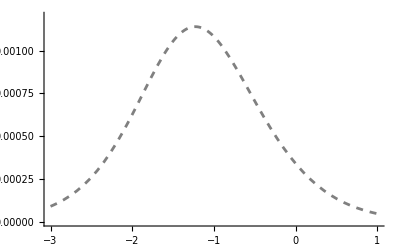

StringJoin::string: String expected at position 1 in fileLocation<>/animationProfile.mp4.

Export::chtype: First argument fileLocation<>/animationProfile.mp4 is not a valid file specification.

StringJoin::string: String expected at position 1 in fileLocation<>/animationCurve.mp4.

Export::chtype: First argument fileLocation<>/animationCurve.mp4 is not a valid file specification.

```mathematica
uphfin = 0;
animatinoAssist = Plot[singleValue[betapf,gammapf,sigmapf,10^uph*.1/20,10^uph,mupf,10^6,20,"None","difference"],{uph,-3,1},AxesOrigin->{-3.1,0},PlotRange->{All,{0,0.0012}},PlotStyle->{Gray,Dashed}];

animation2 = AnimationVideo[Show[animatinoAssist,ListPlot[{{uph,singleValue[betapf,gammapf,sigmapf,10^uph*.1/20,10^uph,mupf,10^6,20,"None","difference"]}},PlotMarkers->{Automatic,Large},PlotStyle->Red]],{uph,-3,1}]
```

```mathematica
Export[fileLocation<>"/animationProfile.mp4",animiation1,"MP4"];
Export[fileLocation<>"/animationCurve.mp4",animation2,"MP4"];
```

### Relative Performance Beta

```mathematica
(*smallest gamma performs worse*)
rp1 = ParallelTable[IntBestUdifferenceRelativePerf[10^beta,2^gamma,1,mu,10^7,20,.1,1,"None"],{gamma,-3,1,1},{beta,0,2,0.1}];
rp2 = ParallelTable[IntBestUdifferenceRelativePerf[10^beta,2^gamma,1,mu,10^7,20,.1,1,"None"],{gamma,-10,-9,1},{beta,0,2,0.1}];
```

```mathematica
Export[fileLocation<>"/rel_performance_beta.mx",rp1];
Export[fileLocation<>"/rel_performance_beta_extra.mx",rp2];
```

```mathematica
rp1 = Import[fileLocation<>"/rel_performance_beta.mx"];
rp2 = Import[fileLocation<>"/rel_performance_beta_extra.mx"];
```

```mathematica
rpbeta = ListLinePlot[rp1,Ticks->{{{1,0},{11,1},{21,2}},{1,1.05,1.06,1.07}},PlotStyle->{{Purple,Opacity[.2]},{Purple,Opacity[.3]},{Purple,Opacity[.4]},{Purple,Opacity[.6]},{Purple,Opacity[.8]},{Purple,Opacity[1]}},AspectRatio->1];
rpbeta2 = ListLinePlot[rp2,Ticks->{{{1,0},{11,1},{21,2}},Automatic},AspectRatio->1];
```

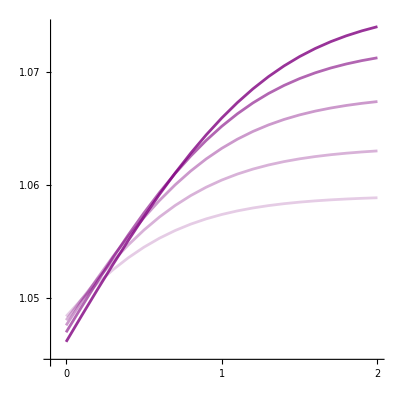

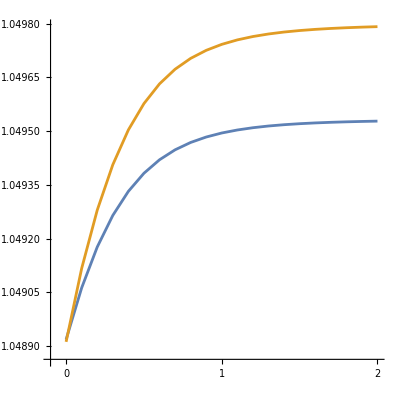

```mathematica
Export[fileLocation<>"/relativePerformanceBeta.eps",rpbeta,"EPS"];
Export[fileLocation<>"/relativePerformanceBeta_extra.eps",rpbeta2,"EPS"];
rpbeta
rpbeta2
```

### Perfect Adaptation Model Performance

```mathematica
Clear[ki,kprod,kub,kis,kb,Dr,Db]
rtotal0 = 10^5;
ki0 = 10^-(3.83);
kis0 = 10^-(2.5)
(*kphi0 = 10^-(0);*)
kub0 = 10^-(0.52);
(*dr/dt = kprod-ki*r-kphi*r+kub*b*)
(*db/dt = -kis*r+kphi*r-kub*b*)
(*something looks wrong*)
rbnd = Solve[{0==kprod-ki*r-kphi*r+kub*b,0==-kis*b+kphi*r-kub*b},{r,b}];
totalR = (rbnd[[1]][[1]][[2]]+rbnd[[1]][[2]][[2]])/.{kub->kub0,kis->kis0,kphi ->0,ki->ki0};
kprod0 = Solve[totalR==rtotal0,kprod][[1]][[1]][[2]];
rbnd = Solve[{0==kprod-ki*r-kphi*r+kub*b,0==-kis*b+kphi*r-kub*b},{r,b}];
totalR = FullSimplify[(rbnd[[1]][[1]][[2]]+rbnd[[1]][[2]][[2]])/.{kub->kub0,kis->kis0,ki->0,kprod->kprod0}];

(*Provides kphi0 which gives similar kprod to what is measured in Dixit et al*)
kphi0 = Solve[totalR==rtotal0,kphi][[1]][[1]][[2]]

rbnd = Solve[{0==kprod-ki*r-kphi*r+kub*b,0==-kis*b+kphi*r-kub*b},{r,b}];
totalR = (rbnd[[1]][[1]][[2]]+rbnd[[1]][[2]][[2]])/.{kub->kub0,kis->kis0,ki->0};

(*Provides kprod in terms of kphi such that Rtotal is 100,000*)
kprod0 = Simplify[Solve[totalR==rtotal0,kprod][[1]][[1]][[2]]]
```

0.00316228

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

0.0149737

0.+(316.228 kphi)/(0.305157+kphi)

```mathematica
(*ki0max = Simplify[Solve[totalR==10^5,ki][[1]][[1]][[2]]]/.{kphi->0};
kphi0max = Simplify[Solve[totalR==10^5,kphi][[1]][[1]][[2]]]/.{ki->0};
phiCoeff =1;
ki0 = ki0max*(1-phiCoeff);
kphi0=kphi0max*phiCoeff;
(rbnd[[1]][[1]][[2]]*ki)/.{ki->ki0,kphi->kphi0,kub->kub0,kis->kis0,rtotal->rtotal0};
(rbnd[[1]][[2]][[2]]*kis)/.{ki->ki0,kphi->kphi0,kub->kub0,kis->kis0,rtotal->rtotal0};
removeFlux = (rbnd[[1]][[1]][[2]]*ki+rbnd[[1]][[2]][[2]]*kis)/.{ki->ki0,kphi->kphi0,kub->kub0,kis->kis0,rtotal->rtotal0};
kprod0 = Solve[totalR==rtotal,kprod][[1]][[1]][[2]]/.{ki->ki0,kphi->kphi0,kub->kub0,kis->kis0,rtotal->rtotal0};
kprod needs to be based on receptor count, kphi,kis, and ki*)

g0 =0.1;
kb0 = 10^-(1.81);
Dr0 = 0.049/2;
Db0 = 0.024/2;
Lc0 = 20;
umax0 =10;
Dr0/(ki0*Lc0^2);
ki0 = 0;
kphi0 = 0.015;
(*u00 = 10^-(0);*)
(*ki0_?NumericQ,kis0_?NumericQ,kprod0_?NumericQ,g0_?NumericQ,kphi0_?NumericQ,kub0_?NumericQ,kb0_?NumericQ,Dr0_?NumericQ,Db0_?NumericQ,u00_?NumericQ,Lc0_?NumericQ,umax_?NumericQ,weight_,type_*)
LHSValsphi = Quiet[ParallelTable[singleValueBasal[ki0,kis0,kprod0/.{kphi->10^kphi0},g0*10^u00/Lc0,10^kphi0,kub0,kb0,Dr0,Db0,10^u00,Lc0,umax0,"None","LHS"],{kphi0,Log10[0.015]-.5,Log10[0.015]+.5,.5},{u00,-2.5,0.5,.05}]];
RHSValsphi = Quiet[ParallelTable[singleValueBasal[ki0,kis0,kprod0/.{kphi->10^kphi0},g0*10^u00/Lc0,10^kphi0,kub0,kb0,Dr0,Db0,10^u00,Lc0,umax0,"None","RHS"],{kphi0,Log10[0.015]-.5,Log10[0.015]+.5,.5},{u00,-2.5,0.5,.05}]];
AverageValsphi = Quiet[ParallelTable[singleValueBasal[ki0,kis0,kprod0/.{kphi->10^kphi0},0,10^kphi0,kub0,kb0,Dr0,Db0,10^u00,Lc0,umax0,"None","average"],{kphi0,Log10[0.015]-.5,Log10[0.015]+.5,.5},{u00,-2.5,0.5,.05}]];
LHSValsphi = (1-LHSValsphi/AverageValsphi)*100;
RHSValsphi = (1-RHSValsphi/AverageValsphi)*100;
AverageValsphi = (1-AverageValsphi/AverageValsphi)*100;
```

NDSolveValue::femibcnd: No DirichletCondition or Robin-type NeumannValue was specified for {b,r}; the result may not be unique.

```mathematica
LHSPoints1 = Transpose[{Array[#&,Length[LHSValsphi[[1]]],{-2.5,0.5}],LHSValsphi[[1]]}];
RHSPoints1 = Transpose[{Array[#&,Length[RHSValsphi[[1]]],{-2.5,0.5}],RHSValsphi[[1]]}];
AveragePoints1 = Transpose[{Array[#&,Length[AverageValsphi[[1]]],{-2.5,0.5}],AverageValsphi[[1]]}];
LHSPoints2 = Transpose[{Array[#&,Length[LHSValsphi[[2]]],{-2.5,0.5}],LHSValsphi[[2]]}];
RHSPoints2 = Transpose[{Array[#&,Length[RHSValsphi[[2]]],{-2.5,0.5}],RHSValsphi[[2]]}];
AveragePoints2 = Transpose[{Array[#&,Length[AverageValsphi[[2]]],{-2.,0.5}],AverageValsphi[[2]]}];
LHSPoints3 = Transpose[{Array[#&,Length[LHSValsphi[[3]]],{-2.5,0.5}],LHSValsphi[[3]]}];
RHSPoints3 = Transpose[{Array[#&,Length[RHSValsphi[[3]]],{-2.5,0.5}],RHSValsphi[[3]]}];
AveragePoints3 = Transpose[{Array[#&,Length[AverageValsphi[[3]]],{-2.5,0.5}],AverageValsphi[[3]]}];
```

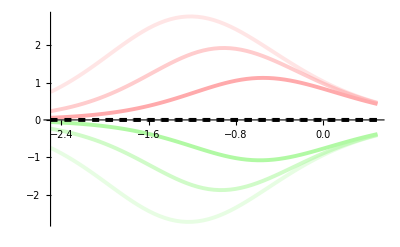

```mathematica
LHSPlot1 = ListLinePlot[LHSPoints1,PlotStyle->{pRed,Opacity[.3],Thickness[.007]}];
RHSPlot1 = ListLinePlot[RHSPoints1,PlotStyle->{pGreen,Opacity[.3],Thickness[.007]}];
AveragePlot1 = ListLinePlot[AveragePoints1,PlotStyle->{Dashed,Black,Opacity[.3],Thickness[.007]}];
LHSPlot2 = ListLinePlot[LHSPoints2,PlotStyle->{pRed,Opacity[.6],Thickness[.007]}];
RHSPlot2 = ListLinePlot[RHSPoints2,PlotStyle->{pGreen,Opacity[.6],Thickness[.007]}];
AveragePlot2 = ListLinePlot[AveragePoints2,PlotStyle->{Dashed,Black,Opacity[.6],Thickness[.007]}];
LHSPlot3 = ListLinePlot[LHSPoints3,PlotStyle->{pRed,Opacity[1],Thickness[.007]}];
RHSPlot3 = ListLinePlot[RHSPoints3,PlotStyle->{pGreen,Opacity[1],Thickness[.007]}];
AveragePlot3 = ListLinePlot[AveragePoints3,PlotStyle->{Dashed,Black,Opacity[1],Thickness[.007]}];
setPoint = Show[{LHSPlot1,RHSPlot1,AveragePlot1,LHSPlot2,RHSPlot2,AveragePlot2,LHSPlot3,RHSPlot3,AveragePlot3},PlotRange->All,AxesOrigin->{-2.5,0}]
Export[fileLocation<>"/setPointphi.eps",setPoint,"EPS"];
```

```mathematica
LHSValsdiff = Quiet[ParallelTable[singleValueBasal[ki0,kis0,kprod0/.{kphi->kphi0},g0*10^u00/Lc0,kphi0,kub0,kb0,Dr0*10^diff,Db0*10^diff,10^u00,Lc0,umax0,"None","LHS"],{diff,-1,1,1},{u00,-2.5,0.5,.05}]];
RHSValsdiff = Quiet[ParallelTable[singleValueBasal[ki0,kis0,kprod0/.{kphi->kphi0},g0*10^u00/Lc0,kphi0,kub0,kb0,Dr0*10^diff,Db0*10^diff,10^u00,Lc0,umax0,"None","RHS"],{diff,-1,1,1},{u00,-2.5,0.5,.05}]];
AverageValsdiff = Quiet[ParallelTable[singleValueBasal[ki0,kis0,kprod0/.{kphi->kphi0},0,kphi0,kub0,kb0,Dr0*10^diff,Db0*10^diff,10^u00,Lc0,umax0,"None","RHS"],{diff,-1,1,1},{u00,-2.5,0.5,.05}]];
LHSValsdiff = (1-LHSValsdiff/AverageValsdiff)*100;
RHSValsdiff = (1-RHSValsdiff/AverageValsdiff)*100;
AverageValsdiff = (1-AverageValsdiff/AverageValsdiff)*100;
```

```mathematica
LHSPoints1 = Transpose[{Array[#&,Length[LHSValsdiff[[1]]],{-2.5,0.5}],LHSValsdiff[[1]]}];
RHSPoints1 = Transpose[{Array[#&,Length[RHSValsdiff[[1]]],{-2.5,0.5}],RHSValsdiff[[1]]}];
AveragePoints1 = Transpose[{Array[#&,Length[AverageValsdiff[[1]]],{-2.5,0.5}],AverageValsdiff[[1]]}];
LHSPoints2 = Transpose[{Array[#&,Length[LHSValsdiff[[2]]],{-2.5,0.5}],LHSValsdiff[[2]]}];
RHSPoints2 = Transpose[{Array[#&,Length[RHSValsdiff[[2]]],{-2.5,0.5}],RHSValsdiff[[2]]}];
AveragePoints2 = Transpose[{Array[#&,Length[AverageValsdiff[[2]]],{-2.,0.5}],AverageValsdiff[[2]]}];
LHSPoints3 = Transpose[{Array[#&,Length[LHSValsdiff[[3]]],{-2.5,0.5}],LHSValsdiff[[3]]}];
RHSPoints3 = Transpose[{Array[#&,Length[RHSValsdiff[[3]]],{-2.5,0.5}],RHSValsdiff[[3]]}];
AveragePoints3 = Transpose[{Array[#&,Length[AverageValsdiff[[3]]],{-2.5,0.5}],AverageValsdiff[[3]]}];
```

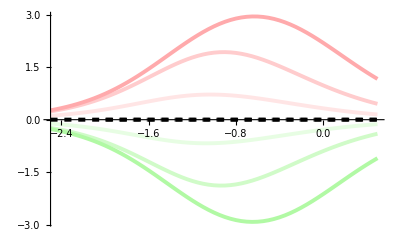

```mathematica
LHSPlot1 = ListLinePlot[LHSPoints1,PlotStyle->{pRed,Opacity[.3],Thickness[.007]}];
RHSPlot1 = ListLinePlot[RHSPoints1,PlotStyle->{pGreen,Opacity[.3],Thickness[.007]}];
AveragePlot1 = ListLinePlot[AveragePoints1,PlotStyle->{Dashed,Black,Opacity[.3],Thickness[.007]}];
LHSPlot2 = ListLinePlot[LHSPoints2,PlotStyle->{pRed,Opacity[.6],Thickness[.007]}];
RHSPlot2 = ListLinePlot[RHSPoints2,PlotStyle->{pGreen,Opacity[.6],Thickness[.007]}];
AveragePlot2 = ListLinePlot[AveragePoints2,PlotStyle->{Dashed,Black,Opacity[.6],Thickness[.007]}];
LHSPlot3 = ListLinePlot[LHSPoints3,PlotStyle->{pRed,Opacity[1],Thickness[.007]}];
RHSPlot3 = ListLinePlot[RHSPoints3,PlotStyle->{pGreen,Opacity[1],Thickness[.007]}];
AveragePlot3 = ListLinePlot[AveragePoints3,PlotStyle->{Dashed,Black,Opacity[1],Thickness[.007]}];
setPoint = Show[{LHSPlot1,RHSPlot1,AveragePlot1,LHSPlot2,RHSPlot2,AveragePlot2,LHSPlot3,RHSPlot3,AveragePlot3},PlotRange->All,AxesOrigin->{-2.5,0}]
Export[fileLocation<>"/setPointdiff.eps",setPoint,"EPS"];
```

### Perfect adaption profile

InterpolatingFunction[…]

InterpolatingFunction[…]

InterpolatingFunction[…]

«1 more identical outputs»

InterpolatingFunction[…]

4685.19

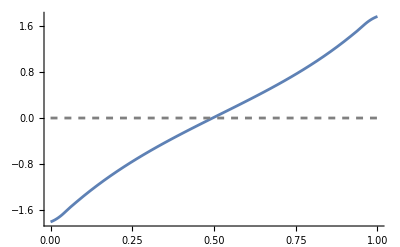

```mathematica
activeProfile1 = ProfileBasal[ki0,kis0,kprod0/.{kphi->kphi0},.1*10^-1/Lc0,kphi0,kub0,kb0,Dr0*10^0,Dr0*10^0,10^-1,Lc0]
avg1 = NIntegrate[activeProfile1[l],{l,0,1}]
p1 = Plot[(activeProfile1[l]-kprod0/kis0/.{kphi->kphi0})/(kprod0/kis0/.{kphi->kphi0})*100,{l,0,1},AxesOrigin->{0,-2}];
p2 = Plot[0,{l,0,1},AxesOrigin->{0,-2},PlotStyle->{Gray,Dashed}];
basalProfile = Show[{p1,p2},PlotRange->All]
Export[fileLocation<>"/basalProfile.eps",basalProfile,"EPS"];
```

### Basal Receptor Model is Perfectly Adaptive

```mathematica
(*Note B is not a function of L*)
Solve[{0==kprod-k0*R+kub*B-L*kb*R,0==k0*R-kis*B-kub*B+L*kb*R},{R,B}]
```

{{R→(kprod (kis+kub))/(kis (k0+kb L)),B→kprod/kis}}

```mathematica
FullSimplify[(kprod (kis+kub))/(kis (k0+kb L))+kprod/kis]
```

(kprod (k0+kis+kub+kb L))/(kis (k0+kb L))